```mathematica
(* Guy Mongelli                                   ChE 400
Prof. Clark                                      11/1/2010   *)
```

```mathematica
(*Assignment #8 *)
```

```mathematica
(* Problem #1 *)
```

```mathematica
(*Part A *)
```

```mathematica
σ=(e*h^2)/(12*ρ*(1-v^2))
```

80.7356

```mathematica
w1[n_,m_]=Simplify[Sqrt[σ((n^4 π^4)/a^4+(m^4 π^4)/b^4)]  (*Hz*)]
```

22.1703 √((m^4+16 n^4)/a^4)

```mathematica
v1[n_,m_]=Simplify[1/(2π)*w1[n,m]]
```

3.52852 √((m^4+16 n^4)/a^4)

```mathematica
(*Part B*)
```

```mathematica
Clear[e,v,ρ,a,b,h]
```

```mathematica
e=30*10^6 *12^2(*lb/ft^2 *);
ρ=490 (*lbm/ft^3*);
a=.5 (*ft*);
v=.3;
b=1 (*ft*);
h=.01(*ft*);
```

```mathematica
F[x_,n_]:=Sin[(n π x)/a]
G[y_,m_]:=Sin[(m π y)/b]
H[t_,n_,m_]:=Cos[w1[n,m]*t]
```

```mathematica
w[x_,y_,t_,n_,m_]:=F[x,n]*G[y,m]*H[t,n,m]
```

```mathematica
w[x,y,t,0,0]
```

0

```mathematica
w[x,y,t,0,1]
```

0

```mathematica
w[x,y,t,1,0]
```

0

```mathematica
Clear[b,a]
```

```mathematica
b=2a;
```

```mathematica
(*In the following table, the modes are displyed for different m and n values.  It is apparent that the modes associated with n or m equal to zero are zero, even if their frequencies are not.  These frequencies are ignored when determining the lowest frequency modes in parts b and c  *)
```

```mathematica
Clear[e,v,ρ,a,b,h]
```

```mathematica
ModesVar=Table[{w[x,y,t,0,i],w[x,y,t,0,i]},{i,0,10}];
TableForm[ModesVar]
```

0 | 0
0 | 0
0 | 0
0 | 0
0 | 0
0 | 0
0 | 0
0 | 0
0 | 0
0 | 0
0 | 0

```mathematica
ModesVar=Table[{w[x,y,t,1,i],w[x,y,t,2,i]},{i,0,10}];
TableForm[ModesVar]
```

0 | 0
Cos[91.4106 √(1/a^4) t] Sin[(π x)/a] Sin[(π y)/b] | Cos[355.418 √(1/a^4) t] Sin[(2 π x)/a] Sin[(π y)/b]
Cos[125.414 √(1/a^4) t] Sin[(π x)/a] Sin[(2 π y)/b] | Cos[365.643 √(1/a^4) t] Sin[(2 π x)/a] Sin[(2 π y)/b]
Cos[218.352 √(1/a^4) t] Sin[(π x)/a] Sin[(3 π y)/b] | Cos[406.993 √(1/a^4) t] Sin[(2 π x)/a] Sin[(3 π y)/b]
Cos[365.643 √(1/a^4) t] Sin[(π x)/a] Sin[(4 π y)/b] | Cos[501.657 √(1/a^4) t] Sin[(2 π x)/a] Sin[(4 π y)/b]
Cos[561.308 √(1/a^4) t] Sin[(π x)/a] Sin[(5 π y)/b] | Cos[658.052 √(1/a^4) t] Sin[(2 π x)/a] Sin[(5 π y)/b]
Cos[803.044 √(1/a^4) t] Sin[(π x)/a] Sin[(6 π y)/b] | Cos[873.41 √(1/a^4) t] Sin[(2 π x)/a] Sin[(6 π y)/b]
Cos[1089.96 √(1/a^4) t] Sin[(π x)/a] Sin[(7 π y)/b] | Cos[1142.79 √(1/a^4) t] Sin[(2 π x)/a] Sin[(7 π y)/b]
Cos[1421.67 √(1/a^4) t] Sin[(π x)/a] Sin[(8 π y)/b] | Cos[1462.57 √(1/a^4) t] Sin[(2 π x)/a] Sin[(8 π y)/b]
Cos[1797.99 √(1/a^4) t] Sin[(π x)/a] Sin[(9 π y)/b] | Cos[1830.5 √(1/a^4) t] Sin[(2 π x)/a] Sin[(9 π y)/b]
Cos[2218.81 √(1/a^4) t] Sin[(π x)/a] Sin[(10 π y)/b] | Cos[2245.23 √(1/a^4) t] Sin[(2 π x)/a] Sin[(10 π y)/b]

```mathematica
ModesVar2=Table[{w[x,y,t,3,i],w[x,y,t,4,i]},{i,0,10}];
TableForm[ModesVar2]
```

0 | 0
Cos[798.44 √(1/a^4) t] Sin[(3 π x)/a] Sin[(π y)/b] | Cos[1419.07 √(1/a^4) t] Sin[(4 π x)/a] Sin[(π y)/b]
Cos[803.044 √(1/a^4) t] Sin[(3 π x)/a] Sin[(2 π y)/b] | Cos[1421.67 √(1/a^4) t] Sin[(4 π x)/a] Sin[(2 π y)/b]
Cos[822.696 √(1/a^4) t] Sin[(3 π x)/a] Sin[(3 π y)/b] | Cos[1432.86 √(1/a^4) t] Sin[(4 π x)/a] Sin[(3 π y)/b]
Cos[873.41 √(1/a^4) t] Sin[(3 π x)/a] Sin[(4 π y)/b] | Cos[1462.57 √(1/a^4) t] Sin[(4 π x)/a] Sin[(4 π y)/b]
Cos[971.708 √(1/a^4) t] Sin[(3 π x)/a] Sin[(5 π y)/b] | Cos[1523.31 √(1/a^4) t] Sin[(4 π x)/a] Sin[(5 π y)/b]
Cos[1128.73 √(1/a^4) t] Sin[(3 π x)/a] Sin[(6 π y)/b] | Cos[1627.97 √(1/a^4) t] Sin[(4 π x)/a] Sin[(6 π y)/b]
Cos[1348.02 √(1/a^4) t] Sin[(3 π x)/a] Sin[(7 π y)/b] | Cos[1787.02 √(1/a^4) t] Sin[(4 π x)/a] Sin[(7 π y)/b]
Cos[1627.97 √(1/a^4) t] Sin[(3 π x)/a] Sin[(8 π y)/b] | Cos[2006.63 √(1/a^4) t] Sin[(4 π x)/a] Sin[(8 π y)/b]
Cos[1965.17 √(1/a^4) t] Sin[(3 π x)/a] Sin[(9 π y)/b] | Cos[2288.7 √(1/a^4) t] Sin[(4 π x)/a] Sin[(9 π y)/b]
Cos[2356.32 √(1/a^4) t] Sin[(3 π x)/a] Sin[(10 π y)/b] | Cos[2632.21 √(1/a^4) t] Sin[(4 π x)/a] Sin[(10 π y)/b]

```mathematica
e=30*10^6 *12^2(*lb/ft^2 *);
ρ=490 (*lbm/ft^3*);
a=.5 (*ft*);
v=.3;
b=1 (*ft*);
h=.01(*ft*);
```

```mathematica
Clear[a,b]
```

```mathematica
b=2a;
```

```mathematica
ModesVar=Table[{w[x,y,t,0,i],w[x,y,t,0,i]},{i,0,10}];
TableForm[ModesVar]
```

0 | 0
0 | 0
0 | 0
0 | 0
0 | 0
0 | 0
0 | 0
0 | 0
0 | 0
0 | 0
0 | 0

```mathematica
ModesVar=Table[{w[x,y,t,1,i],w[x,y,t,2,i]},{i,0,10}];
TableForm[ModesVar]
```

0 | 0
Cos[91.4106 √(1/a^4) t] Sin[(π x)/a] Sin[(π y)/(2 a)] | Cos[355.418 √(1/a^4) t] Sin[(2 π x)/a] Sin[(π y)/(2 a)]
Cos[125.414 √(1/a^4) t] Sin[(π x)/a] Sin[(π y)/a] | Cos[365.643 √(1/a^4) t] Sin[(2 π x)/a] Sin[(π y)/a]
Cos[218.352 √(1/a^4) t] Sin[(π x)/a] Sin[(3 π y)/(2 a)] | Cos[406.993 √(1/a^4) t] Sin[(2 π x)/a] Sin[(3 π y)/(2 a)]
Cos[365.643 √(1/a^4) t] Sin[(π x)/a] Sin[(2 π y)/a] | Cos[501.657 √(1/a^4) t] Sin[(2 π x)/a] Sin[(2 π y)/a]
Cos[561.308 √(1/a^4) t] Sin[(π x)/a] Sin[(5 π y)/(2 a)] | Cos[658.052 √(1/a^4) t] Sin[(2 π x)/a] Sin[(5 π y)/(2 a)]
Cos[803.044 √(1/a^4) t] Sin[(π x)/a] Sin[(3 π y)/a] | Cos[873.41 √(1/a^4) t] Sin[(2 π x)/a] Sin[(3 π y)/a]
Cos[1089.96 √(1/a^4) t] Sin[(π x)/a] Sin[(7 π y)/(2 a)] | Cos[1142.79 √(1/a^4) t] Sin[(2 π x)/a] Sin[(7 π y)/(2 a)]
Cos[1421.67 √(1/a^4) t] Sin[(π x)/a] Sin[(4 π y)/a] | Cos[1462.57 √(1/a^4) t] Sin[(2 π x)/a] Sin[(4 π y)/a]
Cos[1797.99 √(1/a^4) t] Sin[(π x)/a] Sin[(9 π y)/(2 a)] | Cos[1830.5 √(1/a^4) t] Sin[(2 π x)/a] Sin[(9 π y)/(2 a)]
Cos[2218.81 √(1/a^4) t] Sin[(π x)/a] Sin[(5 π y)/a] | Cos[2245.23 √(1/a^4) t] Sin[(2 π x)/a] Sin[(5 π y)/a]

```mathematica
ModesVar2=Table[{w[x,y,t,3,i],w[x,y,t,4,i]},{i,0,10}];
TableForm[ModesVar2]
```

0 | 0
Cos[798.44 √(1/a^4) t] Sin[(3 π x)/a] Sin[(π y)/(2 a)] | Cos[1419.07 √(1/a^4) t] Sin[(4 π x)/a] Sin[(π y)/(2 a)]
Cos[803.044 √(1/a^4) t] Sin[(3 π x)/a] Sin[(π y)/a] | Cos[1421.67 √(1/a^4) t] Sin[(4 π x)/a] Sin[(π y)/a]
Cos[822.696 √(1/a^4) t] Sin[(3 π x)/a] Sin[(3 π y)/(2 a)] | Cos[1432.86 √(1/a^4) t] Sin[(4 π x)/a] Sin[(3 π y)/(2 a)]
Cos[873.41 √(1/a^4) t] Sin[(3 π x)/a] Sin[(2 π y)/a] | Cos[1462.57 √(1/a^4) t] Sin[(4 π x)/a] Sin[(2 π y)/a]
Cos[971.708 √(1/a^4) t] Sin[(3 π x)/a] Sin[(5 π y)/(2 a)] | Cos[1523.31 √(1/a^4) t] Sin[(4 π x)/a] Sin[(5 π y)/(2 a)]
Cos[1128.73 √(1/a^4) t] Sin[(3 π x)/a] Sin[(3 π y)/a] | Cos[1627.97 √(1/a^4) t] Sin[(4 π x)/a] Sin[(3 π y)/a]
Cos[1348.02 √(1/a^4) t] Sin[(3 π x)/a] Sin[(7 π y)/(2 a)] | Cos[1787.02 √(1/a^4) t] Sin[(4 π x)/a] Sin[(7 π y)/(2 a)]
Cos[1627.97 √(1/a^4) t] Sin[(3 π x)/a] Sin[(4 π y)/a] | Cos[2006.63 √(1/a^4) t] Sin[(4 π x)/a] Sin[(4 π y)/a]
Cos[1965.17 √(1/a^4) t] Sin[(3 π x)/a] Sin[(9 π y)/(2 a)] | Cos[2288.7 √(1/a^4) t] Sin[(4 π x)/a] Sin[(9 π y)/(2 a)]
Cos[2356.32 √(1/a^4) t] Sin[(3 π x)/a] Sin[(5 π y)/a] | Cos[2632.21 √(1/a^4) t] Sin[(4 π x)/a] Sin[(5 π y)/a]

```mathematica
(*The mode with the lowest frequency *)
```

```mathematica
a=.5;
```

```mathematica
w[x,y,t,1,1]
```

Cos[365.643 t] Sin[6.28319 x] Sin[3.14159 y]

```mathematica
(*The mode with the third lowest frequency *)
```

```mathematica
w[x,y,t,1,2]
```

Cos[501.657 t] Sin[6.28319 x] Sin[6.28319 y]

```mathematica
(*The mode with the second lowest frequency *)
```

```mathematica
w[x,y,t,2,1]
```

Cos[1421.67 t] Sin[12.5664 x] Sin[3.14159 y]

```mathematica
(*The mode with the fourth lowest frequency *)
```

```mathematica
w[x,y,t,2,2]
```

Cos[1462.57 t] Sin[12.5664 x] Sin[6.28319 y]

```mathematica
a=.5;
```

```mathematica
Element[{n,m},Integers]
```

(n|m)∈Integers

```mathematica
Manipulate[Plot[w[x,y,t,m,n],{x,0,a},PlotRange->1.0],{t,0,2π},{y,0,b},{n,0,4},{m,0,4}]
```

```mathematica
Manipulate[ContourPlot[w[x,y,t,1,1],{x,0,a},{y,0,b},PlotRange->1.0,ContourLabels->True],{t,0,2π}]
```

```mathematica
Manipulate[Plot3D[w[x,y,t,1,1],{x,0,a},{y,0,b},PlotRange->10,ColorFunction->Function[{x,y,z},Hue[.65(1-z)]]],{t,0,2π}]
```

```mathematica
(*Part C *)
```

```mathematica
AngularFrequency=Table[{w1[0,i],w1[1,i],w1[2,i],w1[3,i]},{i,0,10}];
TableForm[AngularFrequency]
```

0 | 354.725 | 1418.9 | 3192.53
88.6813 | 365.643 | 1421.67 | 3193.76
354.725 | 501.657 | 1462.57 | 3212.17
798.132 | 873.41 | 1627.97 | 3290.78
1418.9 | 1462.57 | 2006.63 | 3493.64
2217.03 | 2245.23 | 2632.21 | 3886.83
3192.53 | 3212.17 | 3493.64 | 4514.92
4345.39 | 4359.84 | 4571.18 | 5392.09
5675.61 | 5686.68 | 5850.28 | 6511.89
7183.19 | 7191.94 | 7321.99 | 7860.69
8868.13 | 8875.23 | 8980.93 | 9425.29

```mathematica
LinearFrequency=Table[{v1[0,i],v1[1,i],v1[2,i],v1[3,i]},{i,0,10}];
TableForm[LinearFrequency]
```

0 | 56.4563 | 225.825 | 508.107
14.1141 | 58.1938 | 226.266 | 508.303
56.4563 | 79.8413 | 232.775 | 511.234
127.027 | 139.008 | 259.1 | 523.744
225.825 | 232.775 | 319.365 | 556.03
352.852 | 357.34 | 418.929 | 618.609
508.107 | 511.234 | 556.03 | 718.571
691.59 | 693.89 | 727.525 | 858.177
903.301 | 905.063 | 931.101 | 1036.4
1143.24 | 1144.63 | 1165.33 | 1251.07
1411.41 | 1412.54 | 1429.36 | 1500.08

```mathematica
(*Problem #2  *)
```

```mathematica
C0=10^3/.1;
a=2;
b=3;
```

```mathematica
vup2[m_,n_]:=C0/4(m^2/b^2+n^2/a^2)
```

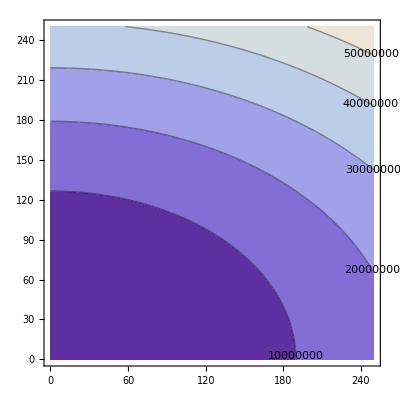

```mathematica
ContourPlot[vup2[m,n],{m,0,250},{n,0,250},ContourLines->All,ContourLabels->True]
```

```mathematica
NSolve[vup2[0,n]==4000^2,{n}]
```

{{n→-160.},{n→160.}}

```mathematica
NSolve[vup2[m,0]==4000^2,{m}]
```

{{m→-240.},{m→240.}}

```mathematica
Solve[vup2[0,n]==2000^2,n]
```

{{n→-80.},{n→80.}}

```mathematica
Solve[vup2[m,0]==2000^2,m]
```

{{m→-120.},{m→120.}}

```mathematica
((π(160)(240)*4000^2)/C0^2)-((π(80)(120)*4000^2)/C0^2)
```

14476.5

```mathematica
ModesNumber=π(((4b^2)/C0^-2)(4*160^2)-((4a^2)/C0^-2)(4*120^2))
```

8.68588×10^14

```mathematica
Area=1/4(-∫_0^160 (4000^2-(C0^2n^2)/(4*a^2))((4*b^2)/C0^2)ⅆn-∫_0^80 (2000^2-(C0^2n^2)/(4*a^2))((4*b^2)/C0^2)ⅆn )
```

863741.

```mathematica
ContourPlot[vup2[m,n],{m,0,250},{n,0,250},ContourLines->All,ContourLabels->True]
```

-Graphics-

```mathematica
(* Problem #3 *)
```

```mathematica
F[x]=Exp[-Abs[x]]*Cos[x]
```

ⅇ^(-Abs[x]) Cos[x]

```mathematica
(*The following transform is incorrect until I learn the correct way to have Mathematica perform transforms as per our notation in class *)
```

```mathematica
Fs[k_]=FourierTransform[F[x],x,k]
```

((2+k^2) √(2/π))/(4+k^4)

```mathematica
(*Part A *)
```

```mathematica
A[k_]=1/π Simplify[∫_(-∞)^∞ Cos[k*x]*F[x]ⅆx,{Real,Element[k,Reals]}]
```

(2 (2+k^2))/((4+k^4) π)

```mathematica
B[k_]=1/π Simplify[∫_(-∞)^∞ Sin[k*x]*F[x]ⅆx,Element[k,Reals]]
```

0

```mathematica
(*f[k] is the fourier transform of F[x] into k-space *)
```

```mathematica
f[k_]=(A[k]-ⅈ*B[k])*π
```

(2 (2+k^2))/(4+k^4)

```mathematica
(*It is off by a factor of sqrt 2pi from mathematica's definition of the transform  *)
```

```mathematica
Fs[k]/f[k]
```

1/(√(2 π))

```mathematica
(*This should be 1 if they were using the same notation *)
```

```mathematica
(*Part b *)
```

```mathematica
(*The integral of the x-space verion of the function *)
```

```mathematica
∫_(-∞)^∞ F[x]ⅆx
```

1

```mathematica
(*The value of my derived fourier transform function (in k-space) at k=0*)
```

```mathematica
f[0]
```

1

```mathematica
(*The value of Mathematica's derived fourier transform function (in k-space) at k=0*)
```

```mathematica
Fs[0]
```

1/(√(2 π))

```mathematica
(*Part C *)
```

```mathematica
∫_(-∞)^∞ Abs[F[x]]^2ⅆx
```

3/4

```mathematica
1/(2π)∫_(-∞)^∞ Abs[f[k]]^2ⅆk
```

3/4

```mathematica
1/(2π)∫_(-∞)^∞ Abs[Fs[k]]^2ⅆk
```

3/(8 π)

```mathematica
(*Problem #4 *)
```

```mathematica
(*Part B *)
```

```mathematica
Finv[x_]=Simplify[1/(2π)∫_(-∞)^∞ f[k]/(-k^2-2)Exp[ⅈ k x]ⅆk,Element[{x,k},Reals]]
```

-1/4 (Cos[x]+Sin[Abs[x]]) (Cosh[x]-Sinh[Abs[x]])

```mathematica
FullSimplify[Finv''[x]-2Finv[x]]
```

1/4 (Cosh[x] (2 Cos[x]+Sin[Abs[x]])+2 Sin[x] Sinh[x]-(3 Cos[x]+2 Sin[Abs[x]]) Sinh[Abs[x]]-2 (Cosh[Abs[x]] Sin[x]+Cos[Abs[x]] Sinh[x]) Abs'[x]+(2 Cos[Abs[x]] Cosh[Abs[x]]+Cosh[x] Sin[Abs[x]]+Cos[x] Sinh[Abs[x]]) Abs'[x]^2+(Cosh[Abs[x]] (Cos[x]+Sin[Abs[x]])+Cos[Abs[x]] (-Cosh[x]+Sinh[Abs[x]])) Abs''[x])

```mathematica
InverseFourierTransform[Re[(((2+k^2) √(2/π))/(4+k^4))/(-k^2-2)],k,x]
```

-1/4 (Cos[x]+Sin[Abs[x]]) (Cosh[x]-Sinh[Abs[x]])

```mathematica
FullSimplify[InverseFourierTransform[(2 (2+k^2))/((4+k^4) π),k,x],x>0]
```

ⅇ^-x √(2/π) Cos[x]

```mathematica
(*Challenge Problem *)
```

```mathematica
rneg[n_]=(ϵ-√(ϵ^2-4((n^2 π^2 C^2)/L^2)))/2
```

1/2 ((C π)/L-√((C^2 π^2)/L^2-(4 C^2 n^2 π^2)/L^2))

```mathematica
ϵ=π C/L
```

(C π)/L

```mathematica
rpos[n_]=(ϵ+√(ϵ^2-4((n^2 π^2 C)/L^2)))/2
```

1/2 ((C π)/L+√((C^2 π^2)/L^2-(4 C n^2 π^2)/L^2))

```mathematica
Fsolution[n_,t_]=Expand[A1*Exp[rpos[n]*t]+A2*Exp[rneg[n]*t]]
```

A1 ⅇ^(1/2 ((C π)/L+√((C^2 π^2)/L^2-(4 C n^2 π^2)/L^2)) t)+A2 ⅇ^(1/2 ((C π)/L-√((C^2 π^2)/L^2-(4 C^2 n^2 π^2)/L^2)) t)

```mathematica
(*A1 should be zero because at t=infinity, y would blow up *)
```

```mathematica
Solve[{Fsolution[n,∞]==0},{A1}]
```

{{A1→-A2 ⅇ^(((C π)/L+√((C (C-4 n^2))/L^2) π) (-∞)+((C π)/L-√(-(C^2 (-1+4 n^2))/L^2) π) ∞)}}